```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
Pe=Import["Pe.txt","List"];
(*Pe runs only upto nn=48*)
```

```mathematica
Clear[V];
μ=50;
nn=24;
(*wc=μ/(nn+1);*)
wc=μ/(nn+5/4);
{me,ϵ,V}={1,0.1,1};
data={};
(*For[V=0.01,V≤π,V+=0.05,*)
For[ϵ=0.0,ϵ≤1,ϵ+=0.1,
{
l=1/Sqrt[me*wc];
En[n_]:=(n+1/2)*wc;
kf[n_]:=Re[Sqrt[2*(μ-En[n])]];
selfenergy[n_]:=(-1/π)*(1/l)*Sum[P1[[n+1,m+1]]*kf[m],{m,0,nn+1}];
smatrix=Table[(selfenergy[n]-selfenergy[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*P2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
kmatrix=Table[(1/π)*(kf[n]-kf[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
M=V*(kmatrix.vmatrix+smatrix);
ΔE[n_]:=(l^4)*(ϵ/4)*Pe[[n+1]];
MX[i_,j_]:=Minors[M][[nn+2-i,nn+2-j]];
δω=-(Sum[(ΔE[i+1]-ΔE[i])*MX[i+1,i+1]/(kf[i+1]-kf[i]),{i,0,nn}])/(Sum[MX[i+1,i+1]/(kf[i+1]-kf[i]),{i,0,nn}]);
(*AppendTo[data,{V*me/π,δω/wc}];*)
AppendTo[data,{ϵ,δω/wc}];
}]
```

```mathematica
line=Fit[data,{1,x},x]
```

-6.6949×10^-17-1.64204 x

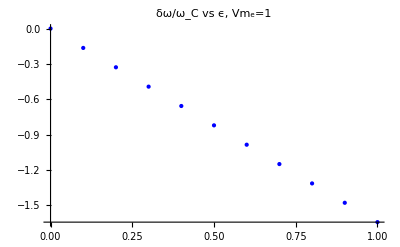

```mathematica
g1=ListPlot[data,PlotStyle->Blue,PlotRange->Automatic,PlotLabel->"δω/ω_C vs ϵ, Vm_e=1"]
```

```mathematica
EmitSound[Play[Sin[1200t+1000*Sqrt[t]+500*t^2],{t,0,3}]]
```

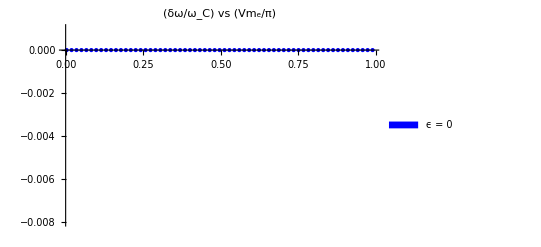

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{-0.008,0.001},PlotLabel->"(δω/ω_C) vs (Vm_e/π)",PlotLegends-> SwatchLegend[{Blue},{"ϵ = 0"}]]
```

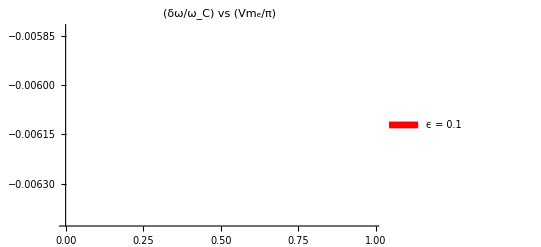

```mathematica
f2=ListPlot[data,PlotStyle->Red,PlotRange->Automatic,PlotLabel->"(δω/ω_C) vs (Vm_e/π)",PlotLegends-> SwatchLegend[{Red},{"ϵ = 0.1"}]]
```

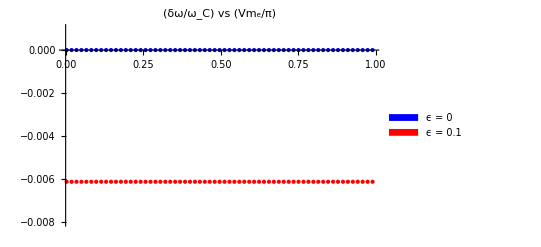

```mathematica
Export["dep_shift_vs_V.png",Show[f1,f2]];
Show[f1,f2]
```

```mathematica
Export["dep_shift_vs_epsilon.png",g1]
```

dep_shift_vs_epsilon.png